## Depict Tiles

```mathematica
TileVertices[step_][or_,dir_,ref_,pt_] := With[{
basicVertices = AnglePath[{
		{step[[2]], -Pi/6+dir*Pi/6},
		{step[[2]], Pi/3},
		{step[[1]], Pi/2},
		{step[[1]], Pi/3},
		{step[[2]], -Pi/2},
		{step[[2]], Pi/3},
		{step[[1]], Pi/2},
		{step[[1]], -Pi/3},
		{step[[2]], Pi/2},
		{step[[2]], -Pi/3},
		{step[[1]], Pi/2},
		{step[[1]], Pi/3},
		{step[[1]], 0}
	}]
},
	Expand[# + or&/@(If[ref,{-#[[1]],#[[2]]},#]&/@((#-basicVertices[[pt]])&/@basicVertices))]
]
```

```mathematica
TileEdges[step_][or_,dir_,ref_,pt_] := Partition[TileVertices[step][or,dir,ref,pt], 2, 1, 1]
```

```mathematica
Tile[step_][or_,dir_,ref_,pt_] := Polygon[TileVertices[step][or,dir,ref,pt]]
```

```mathematica
hatVertices:=TileVertices[{1, Sqrt[3]}];
hatEdges:=TileEdges[{1, Sqrt[3]}];
hat:=Tile[{1, Sqrt[3]}];
```

```mathematica
spectreVertices:=TileVertices[{1,1}];
spectreEdges:=TileEdges[{1,1}];
spectre:=Tile[{1,1}];
```

```mathematica
canonicalHat[or_,dir_,ref_,pt_]:={hatVertices[or,dir,ref,pt][[1]], dir, ref, 1}
```

## Manipulate Cluster

```mathematica
rotateCluster[code_,r_]:=Replace[code,
{
{pos_,dir_,False,pt_}:>{Expand[RotationMatrix[r*Pi/6].pos],Mod[dir+r,12],False,pt},
{pos_,dir_,True,pt_}:>{Expand[RotationMatrix[r*Pi/6].pos],Mod[dir-r,12],True,pt}
},
{1}
];

translateCluster[code_,vec_]:={#1+vec,#2,#3,#4}&@@@code;

placeCluster[pos_,dir_,code_]:=translateCluster[rotateCluster[code,dir],pos];
```

```mathematica
rotateTiling[tiling_, r_] := <|
	"code" -> rotateCluster[tiling["code"], r],
	"controlPoints" -> (Expand[RotationMatrix[r * Pi/6] . #] & /@ tiling["controlPoints"])
|>

translateTiling[tiling_, vec_] := <|
	"code" -> translateCluster[tiling["code"], vec],
	"controlPoints" -> (Expand[# + vec] & /@ tiling["controlPoints"])
|>

placeTiling[pos_, dir_, tiling_] := translateTiling[rotateTiling[tiling, dir], pos];
```

```mathematica
reflectCode[code_]:=Apply[{{-#1,#2}&@@#1,#2,#3/.{True->False,False->True},#4}&,code,{1}];
reflectTiling[tiling_] := <|"code"->reflectCode[tiling["code"]],"controlPoints"->Apply[{-#1,#2}&,tiling["controlPoints"],1]|>
```

## Substitution Rule

```mathematica
substitute[tiling1_,tiling2_]:=
Module[
{
T1,T2,T3,T4,T5,T6,T7
},
T1=placeTiling[tiling1["controlPoints"][[1]],0,tiling1];
T2=placeTiling[T1["controlPoints"][[4]],0,tiling2];
T3=placeTiling[T1["controlPoints"][[6]],4,tiling2];
T4=placeTiling[T1["controlPoints"][[5]],2,tiling2];
T5=placeTiling[T2["controlPoints"][[2]],8,tiling2];
T6=placeTiling[T2["controlPoints"][[3]],10,tiling2];
T7=placeTiling[T2["controlPoints"][[4]],0,tiling2];
Sow[{T1,T2,T3,T4,T5,T6,T7}];
(*Since the control point 1 of T1 is always (0,0), so here it is no need to do subtraction or translation.*)
<|
"tiling1"-><|
"code"->Join@@(#["code"]&/@{T1,T2,T3,T4,T5,T6}),
"controlPoints"->{
T1["controlPoints"][[1]],
T5["controlPoints"][[4]],
T6["controlPoints"][[4]],
T2["controlPoints"][[4]],
T4["controlPoints"][[4]],
T3["controlPoints"][[4]]
}
|>,
"tiling2"-><|
"code"->Join@@(#["code"]&/@{T1,T2,T3,T4,T5,T6,T7}),
"controlPoints"->{
T1["controlPoints"][[1]],
T5["controlPoints"][[4]],
T6["controlPoints"][[4]],
T7["controlPoints"][[4]],
T4["controlPoints"][[4]],
T3["controlPoints"][[4]]
}
|>
|>
]
```

### alternative substitution rule

```mathematica
Asubstitute[tiling1_,tiling2_]:=Module[
{
T1,T2,T3,T4,T5,T6,T7
},
T1=placeTiling[tiling2["controlPoints"][[1]],0,tiling2];
T2=placeTiling[T1["controlPoints"][[4]],0,tiling1];
T3=placeTiling[T1["controlPoints"][[6]],4,tiling2];
T4=placeTiling[T1["controlPoints"][[5]],2,tiling2];
T5=placeTiling[T2["controlPoints"][[2]],8,tiling2];
T6=placeTiling[T2["controlPoints"][[3]],10,tiling2];
T7=placeTiling[T2["controlPoints"][[4]],0,tiling2];
Sow[{T1,T2,T3,T4,T5,T6,T7}];
<|
"tiling1"->translateTiling[<|
"code"->Join@@(#["code"]&/@{T2,T3,T4,T5,T6,T7}),
"controlPoints"->{
T2["controlPoints"][[1]],
T5["controlPoints"][[4]],
T6["controlPoints"][[4]],
T7["controlPoints"][[4]],
T4["controlPoints"][[4]],
T3["controlPoints"][[4]]
}
|>,-T1["controlPoints"][[4]]],
"tiling2"-><|
"code"->Join@@(#["code"]&/@{T1,T2,T3,T4,T5,T6,T7}),
"controlPoints"->{
T1["controlPoints"][[1]],
T5["controlPoints"][[4]],
T6["controlPoints"][[4]],
T7["controlPoints"][[4]],
T4["controlPoints"][[4]],
T3["controlPoints"][[4]]
}
|>
|>
]
```

## Visualization

```mathematica
Options[depictControlPoints]=Join[Options[Graphics],Options[Show],{step->{1,Sqrt[3]},chooseColor->{Blue,Yellow}}];
depictControlPoints[tile_,opt:OptionsPattern[]]:=Show[
	tile["code"]/.{
			{pos_,or_,False,v_}:>
				Graphics[{Opacity[.5],EdgeForm[Black],OptionValue[chooseColor][[1]],Tile[OptionValue[step]][pos,or,False,v]}],
			{pos_,or_,True,v_}:>
				Graphics[{Opacity[.5],EdgeForm[Black],OptionValue[chooseColor][[2]],Tile[OptionValue[step]][pos,or,True,v]}]
	}
	,
Graphics[
{
Red,PointSize[.03],
Point[tile["controlPoints"]],
Line[Partition[tile["controlPoints"],2,1,1]]
}
],
opt
];
```

## Tiles Information

### H2 H1 H7 H8

```mathematica
H2Tiling=<|
"code"->{{{-9/2,-(√3)/2},8,False,3},{{-9/2,-(√3)/2},2,True,11}},
"controlPoints"->{{0,0},{-3/2,(5 √3)/2},{-3,2 √3},{-6,0},{-9/2,-(√3)/2},{-3,0}}
|>;
```

```mathematica
H1Tiling=<|
"code"->{{{0,0},8,False,7}},
"controlPoints"->{{0,0},{-3/2,(5 √3)/2},{-3,2 √3},{-3,√3},{-9/2,-(√3)/2},{-3,0}}
|>;
```

```mathematica
H7Tiling=<|
"code"->{{{-9/2,-(√3)/2},8,False,3},{{-3,0},0,False,7},{{-9/2,-(√3)/2},2,True,11},
{{-15/2,(5 √3)/2},4,False,7},{{-6,0},10,False,9},{{-15/2,(5 √3)/2},8,False,11},{{-15/2,(5 √3)/2},6,False,9}},
"controlPoints"->{{0,0},{-9/2,(7 √3)/2},{-9,4 √3},{-9,√3},{-15/2,-(3 √3)/2},{-3,-2 √3}}
|>;
```

```mathematica
H8Tiling=<|
"code"->{{{-9/2,-(√3)/2},8,False,3},{{-3,0},0,False,7},{{-9/2,-(√3)/2},2,True,11},{{-15/2,(5 √3)/2},4,False,7},
{{-6,0},10,False,9},{{-15/2,(5 √3)/2},8,False,11},{{-15/2,(5 √3)/2},6,False,9},{{-9,2 √3},8,False,9}},
"controlPoints"->{{0,0},{-9/2,(7 √3)/2},{-9,4 √3},{-12,2 √3},{-15/2,-(3 √3)/2},{-3,-2 √3}}
|>;
```

### alternative H7 H8 H2 H1

```mathematica
AH7Tiling=<|
"code"->{{{0,-√3},0,False,7},{{-3/2,-(3 √3)/2},2,True,11},{{-9/2,(3 √3)/2},4,False,7},{{-3,-√3},10,False,9},{{-9/2,(3 √3)/2},8,False,11},{{-9/2,(3 √3)/2},6,False,9},{{-6,√3},8,False,9}},
"controlPoints"->{{0,0},{-3/2,(5 √3)/2},{-6,3 √3},{-9,√3},{-9/2,-(5 √3)/2},{0,-3 √3}}
|>;

AH8Tiling=<|
"code"->{{{-9/2,-(√3)/2},8,False,3},{{-3,0},0,False,7},{{-9/2,-(√3)/2},2,True,11},{{-15/2,(5 √3)/2},4,False,7},
{{-6,0},10,False,9},{{-15/2,(5 √3)/2},8,False,11},{{-15/2,(5 √3)/2},6,False,9},{{-9,2 √3},8,False,9}},
"controlPoints"->{{0,0},{-9/2,(7 √3)/2},{-9,4 √3},{-12,2 √3},{-15/2,-(3 √3)/2},{-3,-2 √3}}
|>;
```

```mathematica
AH2Tiling=<|
"code"->{{{-3/2,-(3 √3)/2},2,True,11},{{-3,-√3},8,False,7}},
"controlPoints"->{{0,0},{-9/2,(3 √3)/2},{-6,√3},{-6,0},{-15/2,-(3 √3)/2},{-6,-√3}}
|>;

AH1Tiling=<|
"code"->{{{0,0},8,False,7}},
"controlPoints"->{{0,0},{-3/2,(5 √3)/2},{-3,2 √3},{-3,√3},{-9/2,-(√3)/2},{-3,0}}
|>;
```

## Let fractal!!!

```mathematica
superTiles=NestList[Values[substitute[#[[1]],#[[2]]]]&,{H2Tiling,H1Tiling},3];
```

```mathematica
superTiles[[3,1]]["code"]//Iconize
```

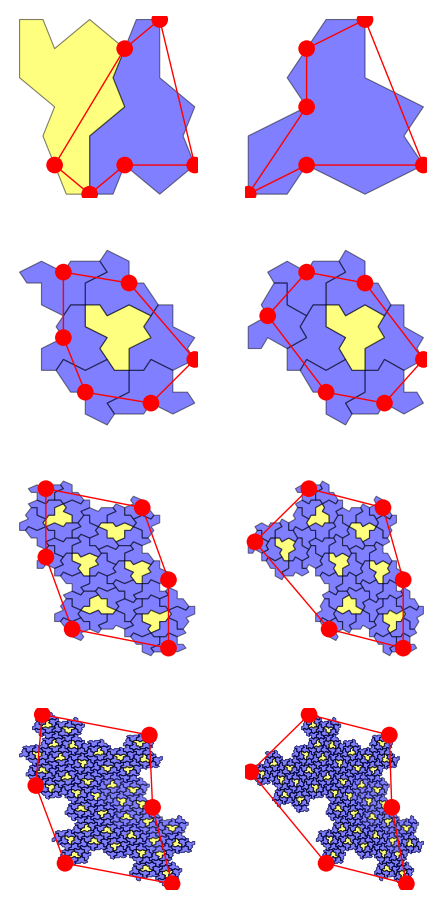

```mathematica
Map[depictControlPoints,superTiles,{2}]//GraphicsGrid
```

## Tiles number

g[n] for number of tiles of tile1. f[n] for number of tiles of tile2

```mathematica
res=First[RSolve[{f[n]==6*f[n-1]+g[n-1],g[n]==5f[n-1]+g[n-1],f[1]==1,g[1]==2},{f[n],g[n]},n]]//FullSimplify
```

{f[n]→(2^(-1-n) (-(7-3 √5)^n (3+√5)-(-3+√5) (7+3 √5)^n))/(√5),g[n]→(2^(-1-n) ((7+3 √5)^n (-15+7 √5)+(7-3 √5)^n (15+7 √5)))/(√5)}

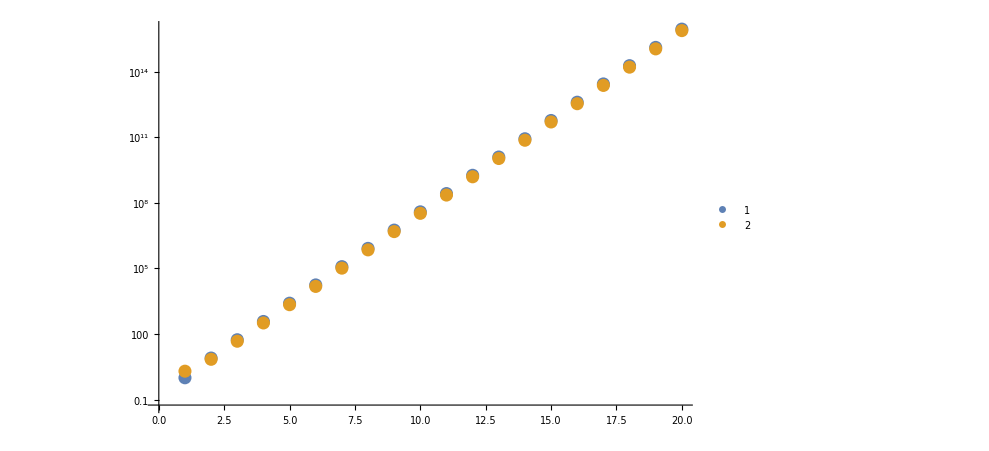

```mathematica
ListLogPlot[Transpose[res[[All,2]]/.{n->#}&/@Range[20]]//Simplify,PlotLegends->Automatic]
```

## Alternative H7 and H8

### From Alternative H7 and H8

It is easy to make a little change on the code, then we can use the same idea to construct the same super-tiles with alternative H7 and H8:

We need to change the control points, and how they are be distinguished in cluster as well. But for this case, there’s a big hole in the middle of the cluster.

```mathematica
superTiles=Reap[NestList[Values[Asubstitute[#[[1]],#[[2]]]]&,{AH7Tiling,AH8Tiling},2]];
```

```mathematica
superTiles[[1,2]][[1]]["code"]//Iconize
```

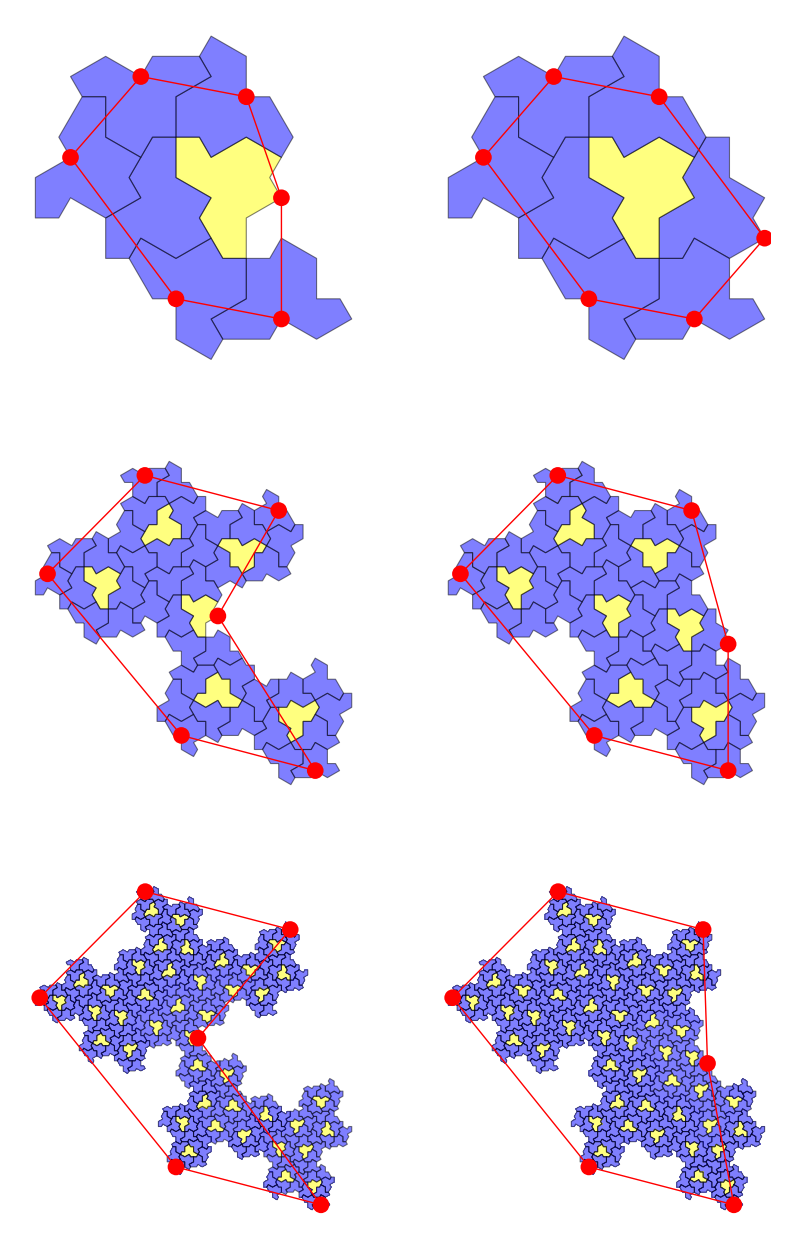

```mathematica
Map[depictControlPoints,superTiles[[1]],{2}]//GraphicsGrid
```

### From Alternative H2 and H1

After observing and trying, we got control points of H2 and H1 as following:

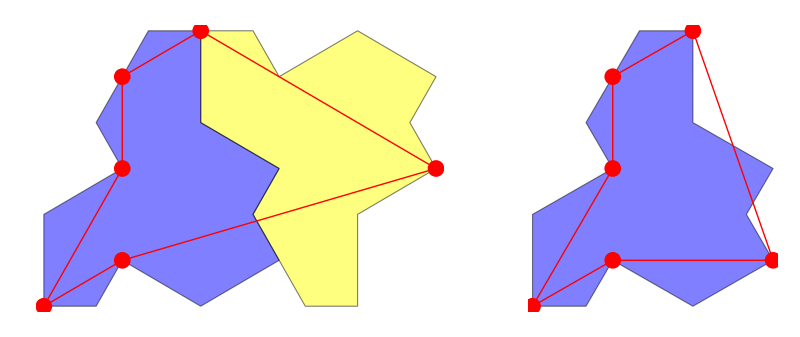

```mathematica
depictControlPoints/@{AH2Tiling,AH1Tiling}//GraphicsRow
```

Only H2 is different from original H2, just like H7 changes into alternative H7.

```mathematica
superTiles=Reap[NestList[Values[Asubstitute[#[[1]],#[[2]]]]&,{AH2Tiling,AH1Tiling},2]];
```

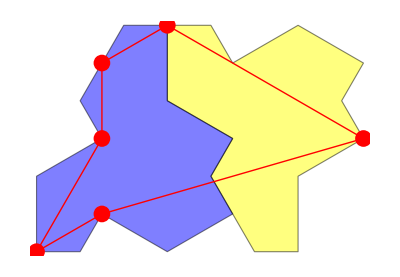
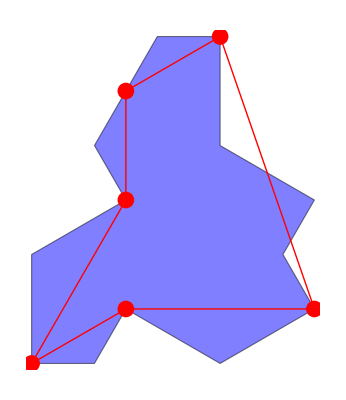
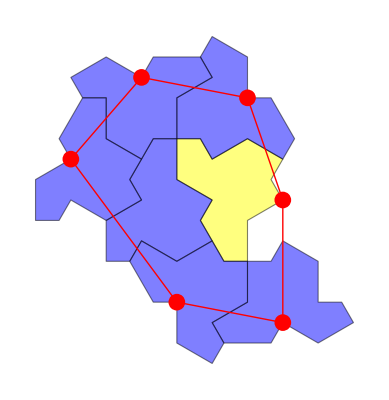
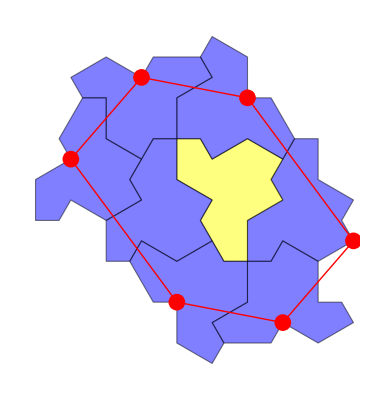
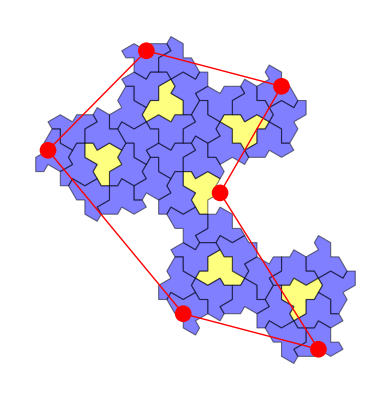
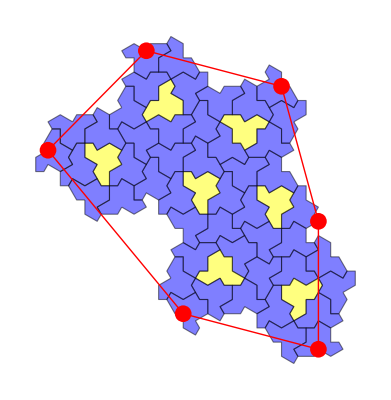
-Graphics- | -Graphics-
H2 | H1
↓
-Graphics- | -Graphics-
H7 | H8
↓
-Graphics- | -Graphics-
H7 super-tile | H8 super-tile

```mathematica
Column[Riffle[MapThread[Grid[{depictControlPoints/@#1,Style[#,Purple,Bold,Italic,14]&/@#2}]&,
{superTiles[[1]],{{"H2","H1"},{"H7","H8"},{"H7 super-tile","H8 super-tile"}}}],Style["↓",60,Red,Bold]],Alignment->Center,Spacings->1]
```

### The process of construction

Original H7 and H8

```mathematica
superTiles=Reap[NestList[Values[substitute[#[[1]],#[[2]]]]&,{H2Tiling,H1Tiling},2]];
```

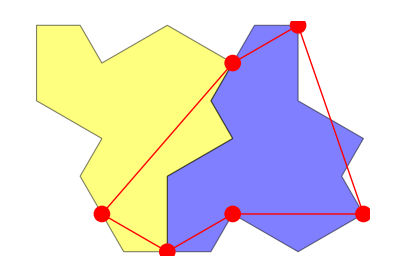
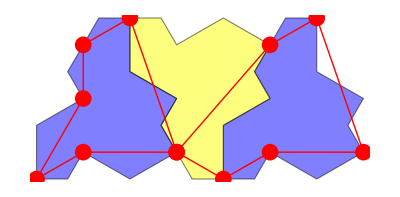
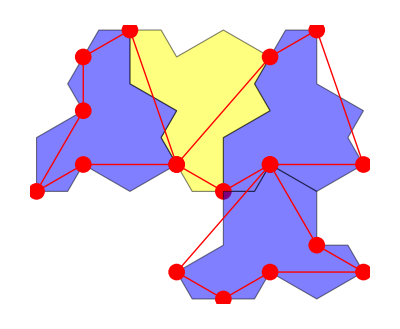
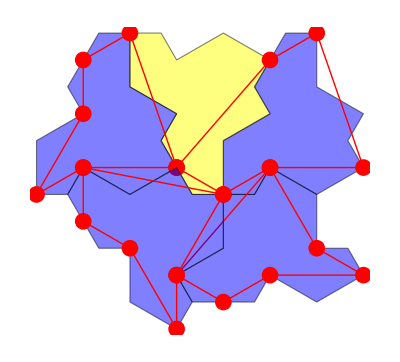
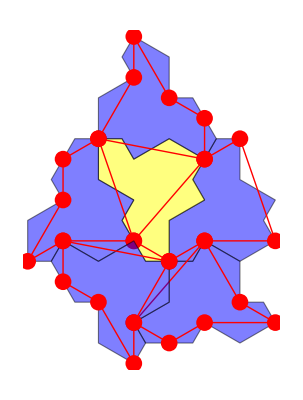
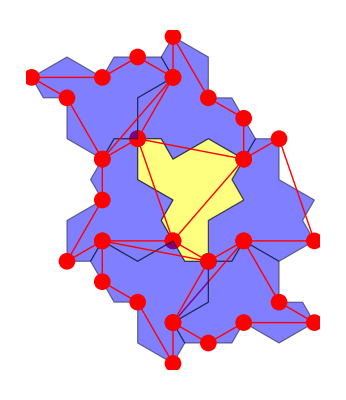
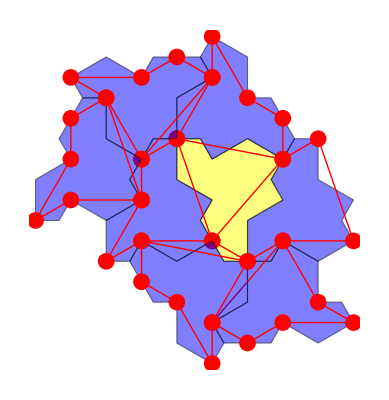
-Graphics-→-Graphics-→-Graphics-→-Graphics-→-Graphics-→-Graphics-→-Graphics-

```mathematica
Row[
Riffle[
(depictControlPoints/@superTiles[[2,1,1,;;#]]//Show)&/@Range[7],
Style["→",32,Purple,Bold]
],Alignment->Center
]
```

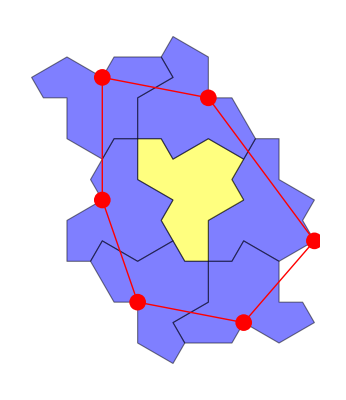
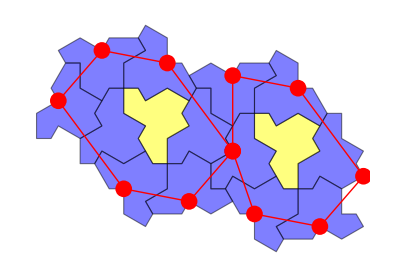
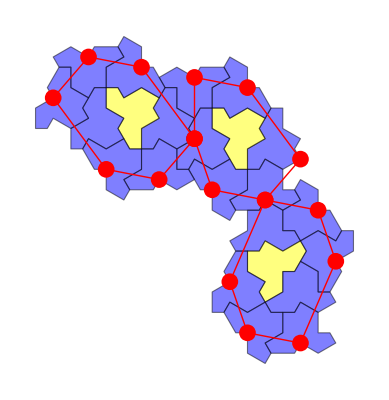
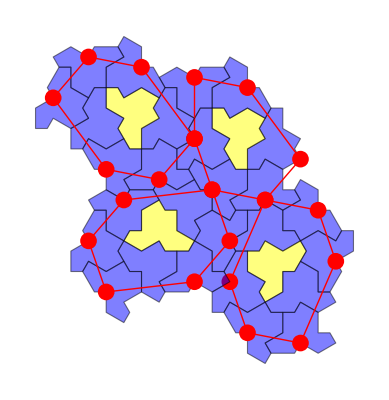
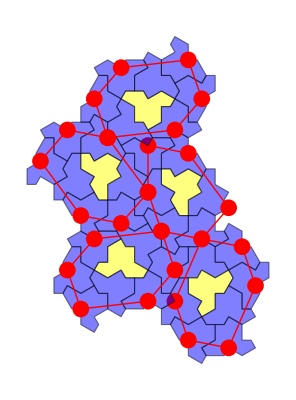
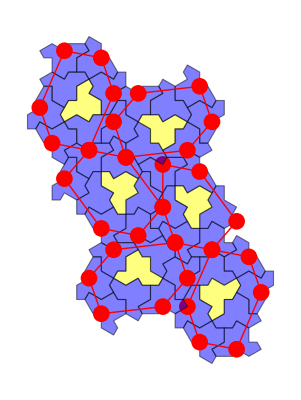
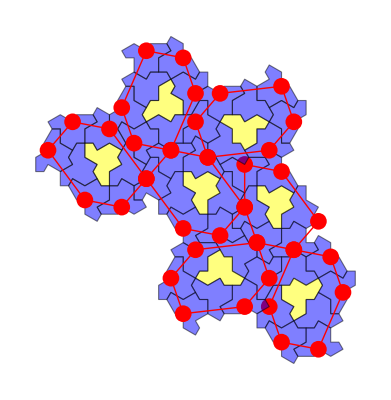
-Graphics-→-Graphics-→-Graphics-→-Graphics-→-Graphics-→-Graphics-→-Graphics-

```mathematica
Row[
Riffle[
(depictControlPoints/@superTiles[[2,1,2,;;#]]//Show)&/@Range[7],
Style["→",32,Purple,Bold]
],Alignment->Center
]
```

alternative H7 and H8

```mathematica
AsuperTiles=Reap[NestList[Values[Asubstitute[#[[1]],#[[2]]]]&,{AH2Tiling,AH1Tiling},2]];
```

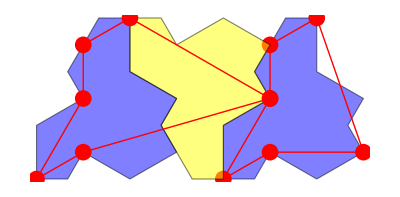
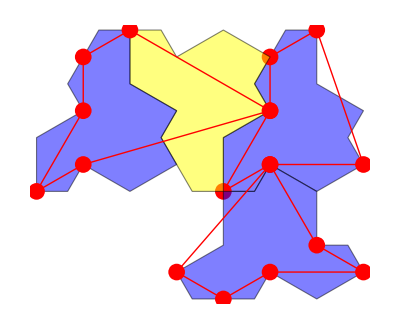
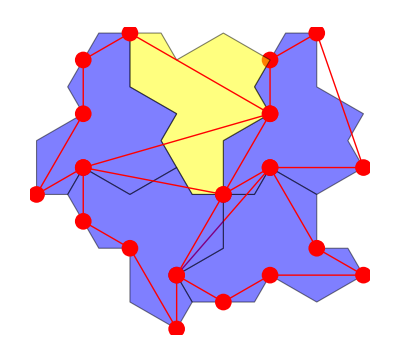
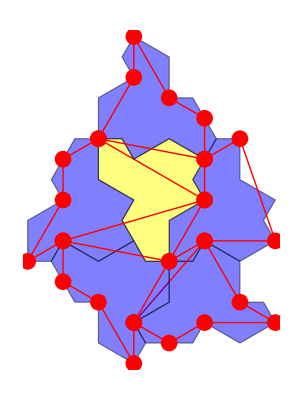
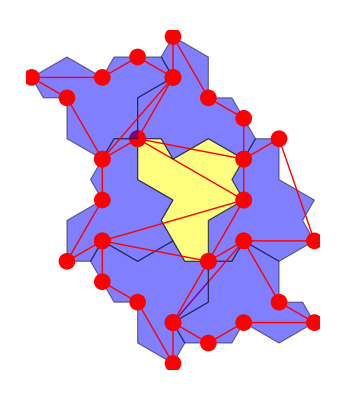
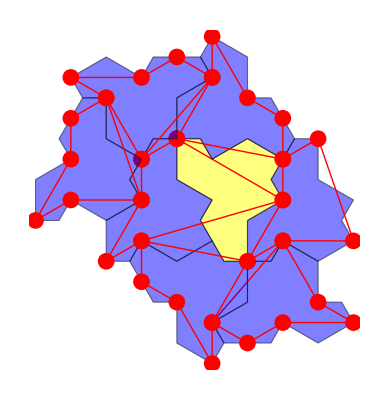
-Graphics-→-Graphics-→-Graphics-→-Graphics-→-Graphics-→-Graphics-→-Graphics-

```mathematica
Row[
Riffle[
(depictControlPoints/@AsuperTiles[[2,1,1,;;#]]//Show)&/@Range[7],
Style["→",32,Purple,Bold]
],Alignment->Center
]
```

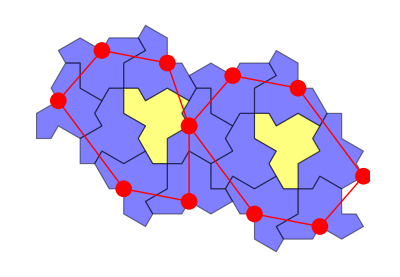
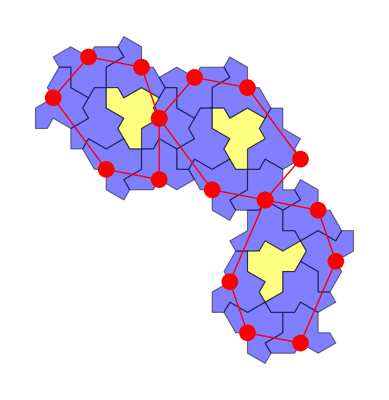
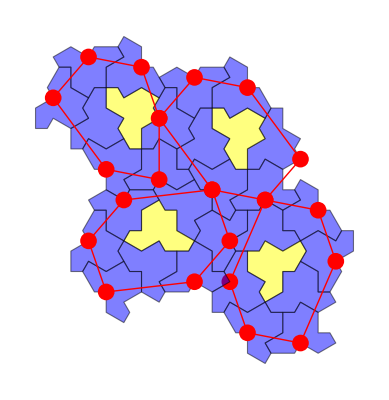
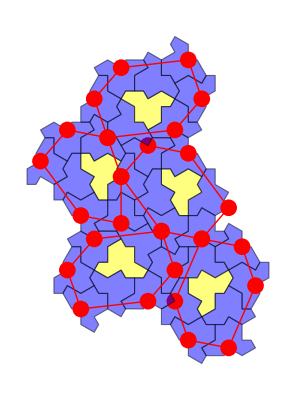
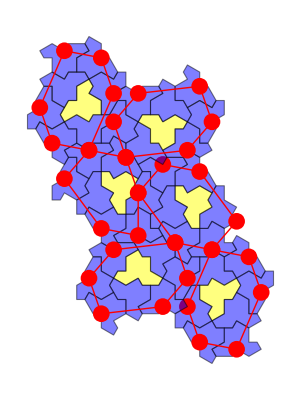
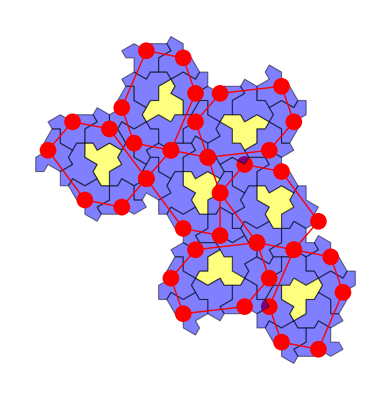
-Graphics-→-Graphics-→-Graphics-→-Graphics-→-Graphics-→-Graphics-→-Graphics-

```mathematica
Row[
Riffle[
(depictControlPoints/@AsuperTiles[[2,1,2,;;#]]//Show)&/@Range[7],
Style["→",32,Purple,Bold]
],Alignment->Center
]
```

### Why they are equivalent?

Each super-tile consists of two sorts of clusters and 7 in total, 6 of which are like original H8, and the other one is like original H7.

The interesting thing is, original H7 must have a translated version of H8 as its partner, like this:

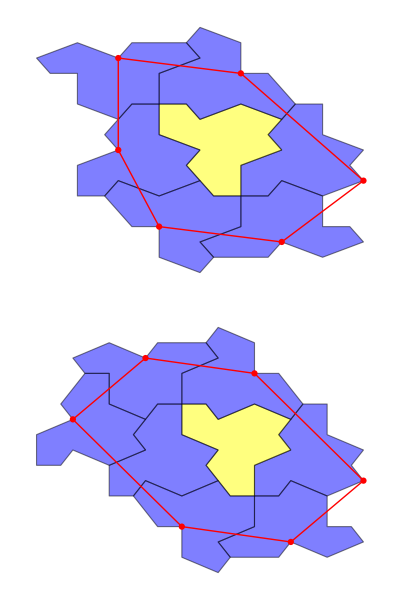
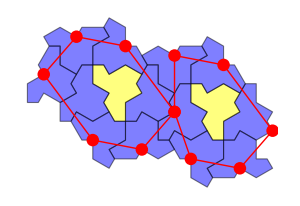
-Graphics-→-Graphics-

```mathematica
Row[
{Column[{#1,#2}],
Style["→",32,Purple,Bold],
Show[#1,#2,ImageSize->300]},"           "]&@@(depictControlPoints[#,ImageSize->150]&/@superTiles[[2,1,2,;;2]])
```

The figure above is original H7 and H8, and the following is alternative H7 and H8:

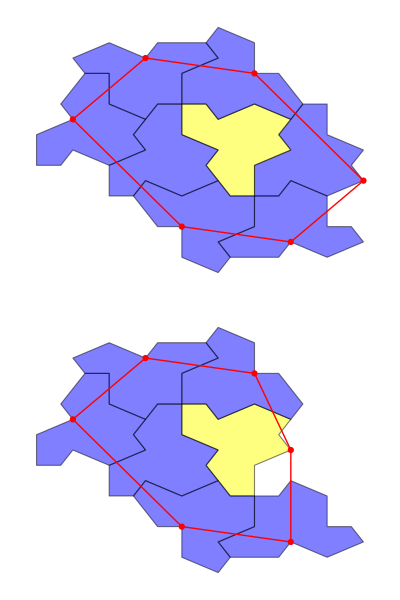
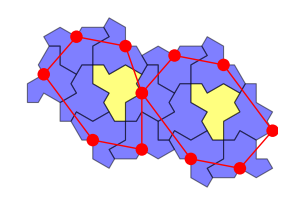
-Graphics-→-Graphics-

```mathematica
Row[
{Column[{#1,#2}],
Style["→",32,Purple,Bold],
Show[#1,#2,ImageSize->300]},"           "]&@@(depictControlPoints[#,ImageSize->150]&/@AsuperTiles[[2,1,2,;;2]])
```

You can tell I’m not cheating by using the same merged cluster figure from different control points.

Since H7 must merge with H8 (it looks true), these two definition both works to construct super-tile by this way.

### H7 and H8 in a big cluster

And there are some clues about it may have been shown in previous discussion, that is we cannot distinguish H7 or H8 from a cluster big enough, like when I try to find all H7 and H8 in a big cluster. There are some delicate things happening here:

-Graphics-

These are all boundaries for H8 in this cluster, derivate by findByWalk function, which would walk from the reflected hat with certain steps to the boundary and begin to walk along the boundary with certain edge vectors and tags to find the boundary of H8. In the red circles, there are two special hats are surrounded by blue boundary respectively. That is because findByWalk function can’t distinguish H7 plus this hat with H8.

And about to distinguish them, we have to ways to divide the clusters in the red circle. One way is see them as a pair of original H7 and H8, the other is a pair of alternative H7 and H8.

### Brief Conclusion

Original H7 and H8 are equivalent to alternative H7 and H8 to construct big cluster since one H7 is always with a H8 to merge a pair, and this pair can be regarded as a pair as alternative H7 and H8 as well.